```mathematica
{
{0,1,0},
{1,0,0},
{0,0,1}
}.{
{0,1,0},
{0,0,1},
{1,0,0}
}.{a1,a2,a3}
```

{a3,a2,a1}

```mathematica
x1
```

```mathematica
{{0,0,1},{0,1,0},{1,0,0}}//MatrixForm
```

(0 | 0 | 1
0 | 1 | 0
1 | 0 | 0)

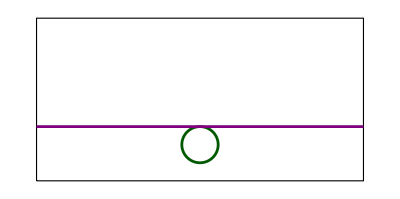

-Graphics3D-

```mathematica
x[t_]:={t,π/3}
y[θ_]:={π,2π/9}+π/9{Cos[θ],Sin[θ]}
spherical[θ_,ϕ_]:={Cos[θ]Sin[ϕ],Sin[θ] Sin[ϕ],Cos[ϕ]}
Show[
Graphics[{EdgeForm[Black],White,Rectangle[{0,0},{2π,π}]}],
ParametricPlot[
y[θ],{θ,0,2π},PlotStyle->DarkGreen
],
ParametricPlot[
x[t],{t,0,2π},PlotStyle->Purple
]
]
Show[
ParametricPlot3D[spherical[θ,ϕ],{θ,0,2π},{ϕ,0,π}],
ParametricPlot3D[spherical@@x[t],{t,0,2π}],
ParametricPlot3D[spherical@@y[t],{t,0,2π}]
]
```